## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PGI";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_PGI_TEST_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{g6p,Null,Keq substrate}

{0.364,Keq value}

{g6p,Km or S05 substrate}

{0.001018,Km or S05 value}

{f6p,Km or S05 substrate}

{0.000078,Km or S05 value}

{pep,Inhibition or activation constant substrate}

{0.00026,Inhibition or activation constant value}

(g6p^c⇌f6p^c)^PGI

Null; Null

Structure: 2

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p,Null | 0.364 | 0.3458
0.3822 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.001018 | 0.000876
0.00116 |  | M | 7.2 | 23 | mopskoh | 0.1 | 
1 | f6p | 0.000078 | 0.000069
0.000087 |  | M | 7.2 | 23 | mopskoh | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pep | 0.00026 | 0.000247
0.000273 |  | Competitive | f6p | 0.000078 |  | 7.2 | 23 | mopskoh | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = Null;
inhibitionPriorities={1};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(g6p^c⇌f6p^c)^PGI

Null; Null

Structure: 2

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p,Null | 0.364 | 0.3458
0.3822 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | g6p | 0.001018 | 0.000876
0.00116 |  | M | 7.2 | 23 | mopskoh | 0.1 | 
1 | f6p | 0.000078 | 0.000069
0.000087 |  | M | 7.2 | 23 | mopskoh | 0.1 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | pep | 0.00026 | 0.000247
0.000273 |  | Competitive | f6p | 0.000078 |  | 7.2 | 23 | mopskoh | 0.1 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGI[c] + g6p[c] <=> E_PGI[c]&g6p",
				"E_PGI[c]&g6p <=> E_PGI[c]&f6p",
				"E_PGI[c]&f6p <=> E_PGI[c] + f6p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PGI^c)_^+g6p^c⇌(PGI^c&g6p^c)_^)^PGI1,((PGI^c&f6p^c)_^⇌(PGI^c)_^+f6p^c)^PGI2,((PGI^c&g6p^c)_^⇌(PGI^c&f6p^c)_^)^PGI3}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGI^c)_^+g6p^c⇌(PGI^c&g6p^c)_^)^PGI1,Overscript[(PGI^c&f6p^c)_^⇌(PGI^c)_^+f6p^c, PGI2],((PGI^c&g6p^c)_^⇌(PGI^c&f6p^c)_^)^PGI3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{g6p^c→0}

{f6p^c→0}

{g6p^c→∞}

{f6p^c→∞}

Added inhibition reactions:

{((PGI^c)_^+pep^c⇌(PGI^c&pep^c)_^)^PGI_Kic_pep_1_f6p}

Generating flux equation...

{((PGI^c&g6p^c)_^-((PGI^c&f6p^c)_^)/K_PGI3) Volume_c k_PGI3^⟶}

Volume_c (-(PGI^c&f6p^c)_^ k_PGI3^⟵+(PGI^c&g6p^c)_^ k_PGI3^⟶)

1

2

3

0.056211

4

0.00034

5

0.0001

Simplifying...

6

0.043641

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={(*{1, (Subscript[k, GAPD1]^⟶Subscript[k, GAPD2]^⟶Subscript[k, GAPD3]^⟶Subscript[k, GAPD4]^⟶Subscript[k, GAPD5]^⟶)/(Subscript[k, GAPD1]^⟵Subscript[k, GAPD2]^⟵Subscript[k, GAPD3]^⟵Subscript[k, GAPD4]^⟵Subscript[k, GAPD5]^⟵), 4.25*10^2,{0.9*4.25*10^2,1.1*4.25*10^2}}*)};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating inhibition data...

{k_PGI_Kic_pep_1_f6p^⟵/k_PGI_Kic_pep_1_f6p^⟶}

```mathematica
Print[inhibitionList]
```

{{1,Kic,pep,0.00026,{0.000247,0.000273},{},{{Competitive,f6p,0.000078}},,7.2,23,{{mopskoh,0.1}},{}}}

```mathematica
Print[bufferInfo]
```

{{{trishcl,Tris-HCl},8.14,1,0},{{tris,Tris},8.14,1,0},{{trisac,Tris-acetate},8.14,1,0},{{edta,EDTA},Null,Null,Null},{{tric,Tricine},8.07,0,-1},{{tricna,Tricine-Na},8.07,0,-1},{{hepesnaoh,Hepes-NaOH},7.5,0,-1},{{pipeskoh,PIPES-KOH},6.64,-1,-2},{{kpi,KPO4},6.88,-1,-2},{{napi,sodium phosphate},6.88,-1,-2},{{nakpi,Na+/K+ phosphate},6.88,-1,-2},{{chesk,CHES-K},9.37,0,-1},{{hepes,Hepes},7.5,0,-1},{{hepesbtp,HEPES-BTP},Null,Null,Null},{{pipes,Pipes},6.64,-1,-2},{{mops,MOPS},7.12,0,-1},{{mopsnaoh,MOPS/NaOH},7.12,0,-1},{{mopskoh,MOPS-KOH},7.12,0,-1},{{mes,MES},6.14,0,-1},{{netmphn,N-ethylmorpholine},7.83,1,0},{{detam,diethanolamine},8.95,1,0},{{glygly,glycylglycine},8.2,0,-1},{{imdzcl,imidazole-Cl},7.06,1,0},{{imdz_MIXED,mixed imidazoles},Null,Null,Null},{{24dmid,2,4-dimethylimidazole},Null,Null,Null},{{teoa,triethanolamine},7.83,1,0},{{teoahcl,triethanolamine-HCl},7.83,1,0},{{pi_buffer,Phosphoric acid},7.198,-1,-2},{{dtpa,DTPA},Null,Null,Null}}

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	g6p[c]	pep[c]	param_PGI_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt"	0.364
1	0	0.00010180000000000001	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.09090909090909091
1	0	0.00016134212699254143	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.13680688860321005
1	0	0.00025571003872767523	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.20076000891310172
1	0	0.00040527309962346035	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.2847472489508015
1	0	0.0006423145766808373	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.3868631798468572
1	0	0.0010180000000000002	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.5
1	0	0.0016134212699254144	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.6131368201531431
1	0	0.0025571003872767524	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.7152527510491985
1	0	0.0040527309962346035	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.7992399910868984
1	0	0.006423145766808372	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.8631931113967901
1	0	0.010180000000000002	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt"	0.9090909090909091
1	7.800000000000007e-6	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.09090909090909098
1	0.000012362166901196701	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.13680688860321016
1	0.000019592714165774757	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.200760008913102
1	0.000031052359303172786	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.28474724895080145
1	0.0000492146728694551	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.3868631798468571
1	0.00007800000000000007	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.5000000000000002
1	0.00012362166901196703	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.6131368201531434
1	0.00019592714165774758	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.7152527510491989
1	0.0003105235930317282	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.7992399910868984
1	0.0004921467286945509	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.86319311139679
1	0.0007800000000000007	0	0	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.9090909090909093
1	7.800000000000007e-6	0	0.00013	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.06250000000000006
1	0.00002466576574931338	0	0.00013	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.17411239489546845
1	0.00007800000000000007	0	0.00013	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.4000000000000002
1	0.00024665765749313384	0	0.00013	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.6782688399674107
1	0.0007800000000000007	0	0.00013	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.8695652173913044
1	7.800000000000007e-6	0	0.00026	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.04761904761904766
1	0.00002466576574931338	0	0.00026	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.13652705949581442
1	0.00007800000000000007	0	0.00026	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.33333333333333354
1	0.00024665765749313384	0	0.00026	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.6125741132772071
1	0.0007800000000000007	0	0.00026	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.8333333333333334
1	7.800000000000007e-6	0	0.00052	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.03225806451612906
1	0.00002466576574931338	0	0.00052	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.09535767393826004
1	0.00007800000000000007	0	0.00052	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.25000000000000017
1	0.00024665765749313384	0	0.00052	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.5131670194948623
1	0.0007800000000000007	0	0.00052	1	7.2	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt"	0.7692307692307694
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026
1	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt"	0.00026

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
0.7	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
0.7	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
0.7	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
0.7	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
0.7	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
0.7	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
0.7	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
0.7	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
0.7	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
0.7	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
0.7	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268.6249933354222
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
0.7	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
0.7	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
0.7	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
0.7	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
0.7	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
0.7	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
0.7	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
0.7	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
0.7	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
0.7	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
0.7	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	268
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	8
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateFor_g6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/relRateRev_f6p.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PGI_TEST_typeII/input/inhibRatio_pep_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.395981899671
best_fit: 1.02564882594
best_fit: 0.167323143266
best_fit: 0.141536987865
best_fit: 1.07470065751

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_TRPS3_TEST_typeII/input/TRPS3.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | haldaneRatio_1 | 9.43634×10^-13 | 8.90445×10^-25 | 7.90923×10^-13 | 2.17287×10^-10 | 0.364 | 0.364
1 | relRateFor_g6p | 3.52895×10^-12 | 1.24535×10^-23 | 7.38715×10^-13 | 8.12586×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_g6p | 3.35088×10^-12 | 1.12284×10^-23 | 1.05557×10^-12 | 7.71578×10^-10 | 0.136807 | 0.136807
1 | relRateFor_g6p | 3.10263×10^-12 | 9.62631×10^-24 | 1.43424×10^-12 | 7.14406×10^-10 | 0.20076 | 0.20076
1 | relRateFor_g6p | 2.77645×10^-12 | 7.70865×10^-24 | 1.82043×10^-12 | 6.39315×10^-10 | 0.284747 | 0.284747
1 | relRateFor_g6p | 2.3801×10^-12 | 5.66486×10^-24 | 2.12019×10^-12 | 5.48047×10^-10 | 0.386863 | 0.386863
1 | relRateFor_g6p | 1.941×10^-12 | 3.76749×10^-24 | 2.23466×10^-12 | 4.46931×10^-10 | 0.5 | 0.5
1 | relRateFor_g6p | 1.50183×10^-12 | 2.25548×10^-24 | 2.1203×10^-12 | 3.45813×10^-10 | 0.613137 | 0.613137
1 | relRateFor_g6p | 1.10542×10^-12 | 1.22196×10^-24 | 1.82054×10^-12 | 2.54532×10^-10 | 0.715253 | 0.715253
1 | relRateFor_g6p | 7.79377×10^-13 | 6.07428×10^-25 | 1.4343×10^-12 | 1.79458×10^-10 | 0.79924 | 0.79924
1 | relRateFor_g6p | 5.31047×10^-13 | 2.82011×10^-25 | 1.05549×10^-12 | 1.22277×10^-10 | 0.863193 | 0.863193
1 | relRateFor_g6p | 3.52919×10^-13 | 1.24552×10^-25 | 7.38742×10^-13 | 8.12617×10^-11 | 0.909091 | 0.909091
1 | relRateRev_f6p | 4.34008×10^-12 | 1.88363×10^-23 | 9.08482×10^-13 | 9.9933×10^-10 | 0.0909091 | 0.0909091
1 | relRateRev_f6p | 4.12093×10^-12 | 1.6982×10^-23 | 1.29813×10^-12 | 9.48876×10^-10 | 0.136807 | 0.136807
1 | relRateRev_f6p | 3.81561×10^-12 | 1.45589×10^-23 | 1.76384×10^-12 | 8.78581×10^-10 | 0.20076 | 0.20076
1 | relRateRev_f6p | 3.41449×10^-12 | 1.16587×10^-23 | 2.23876×10^-12 | 7.86229×10^-10 | 0.284747 | 0.284747
1 | relRateRev_f6p | 2.92716×10^-12 | 8.56826×10^-24 | 2.60747×10^-12 | 6.74003×10^-10 | 0.386863 | 0.386863
1 | relRateRev_f6p | 2.38698×10^-12 | 5.69767×10^-24 | 2.74814×10^-12 | 5.49627×10^-10 | 0.5 | 0.5
1 | relRateRev_f6p | 1.84683×10^-12 | 3.41077×10^-24 | 2.60736×10^-12 | 4.25249×10^-10 | 0.613137 | 0.613137
1 | relRateRev_f6p | 1.35936×10^-12 | 1.84785×10^-24 | 2.23876×10^-12 | 3.13003×10^-10 | 0.715253 | 0.715253
1 | relRateRev_f6p | 9.58483×10^-13 | 9.1869×10^-25 | 1.76392×10^-12 | 2.207×10^-10 | 0.79924 | 0.79924
1 | relRateRev_f6p | 6.53158×10^-13 | 4.26615×10^-25 | 1.29818×10^-12 | 1.50393×10^-10 | 0.863193 | 0.863193
1 | relRateRev_f6p | 4.3391×10^-13 | 1.88278×10^-25 | 9.08273×10^-13 | 9.99101×10^-11 | 0.909091 | 0.909091
1 | relRateRev_f6p | 4.21996×10^-12 | 1.7808×10^-23 | 6.07306×10^-13 | 9.71689×10^-10 | 0.0625 | 0.0625
1 | relRateRev_f6p | 3.71758×10^-12 | 1.38204×10^-23 | 1.49039×10^-12 | 8.55994×10^-10 | 0.174112 | 0.174112
1 | relRateRev_f6p | 2.70084×10^-12 | 7.29453×10^-24 | 2.48757×10^-12 | 6.21891×10^-10 | 0.4 | 0.4
1 | relRateRev_f6p | 1.44817×10^-12 | 2.09721×10^-24 | 2.26175×10^-12 | 3.33459×10^-10 | 0.678269 | 0.678269
1 | relRateRev_f6p | 5.87093×10^-13 | 3.44678×10^-25 | 1.1755×10^-12 | 1.35183×10^-10 | 0.869565 | 0.869565
1 | relRateRev_f6p | 4.15712×10^-12 | 1.72816×10^-23 | 4.55816×10^-13 | 9.57213×10^-10 | 0.047619 | 0.047619
1 | relRateRev_f6p | 3.76887×10^-12 | 1.42044×10^-23 | 1.18483×10^-12 | 8.67835×10^-10 | 0.136527 | 0.136527
1 | relRateRev_f6p | 2.90995×10^-12 | 8.46781×10^-24 | 2.23349×10^-12 | 6.70047×10^-10 | 0.333333 | 0.333333
1 | relRateRev_f6p | 1.69112×10^-12 | 2.85989×10^-24 | 2.38531×10^-12 | 3.89392×10^-10 | 0.612574 | 0.612574
1 | relRateRev_f6p | 7.27585×10^-13 | 5.29379×10^-25 | 1.39611×10^-12 | 1.67533×10^-10 | 0.833333 | 0.833333
1 | relRateRev_f6p | 4.09228×10^-12 | 1.67468×10^-23 | 3.03958×10^-13 | 9.42271×10^-10 | 0.0322581 | 0.0322581
1 | relRateRev_f6p | 3.82538×10^-12 | 1.46336×10^-23 | 8.39939×10^-13 | 8.8083×10^-10 | 0.0953577 | 0.0953577
1 | relRateRev_f6p | 3.17146×10^-12 | 1.00582×10^-23 | 1.82565×10^-12 | 7.3026×10^-10 | 0.25 | 0.25
1 | relRateRev_f6p | 2.05863×10^-12 | 4.23796×10^-24 | 2.4325×10^-12 | 4.74017×10^-10 | 0.513167 | 0.513167
1 | relRateRev_f6p | 9.75761×10^-13 | 9.5211×10^-25 | 1.72828×10^-12 | 2.24677×10^-10 | 0.769231 | 0.769231
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026
1 | inhibRatio_pep_1 | 8.18012×10^-13 | 6.69144×10^-25 | 4.89788×10^-16 | 1.8838×10^-10 | 0.00026 | 0.00026

### Simulated Data and Best Fit Data Plot

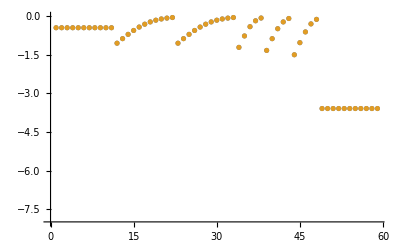

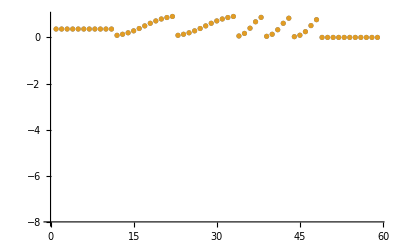

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

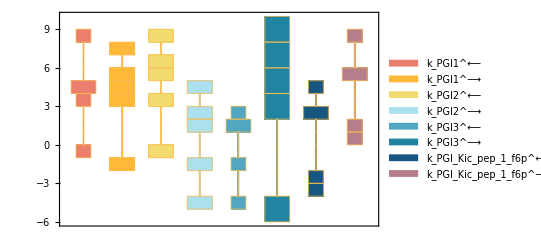

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

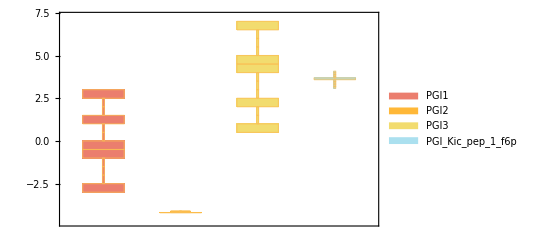

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

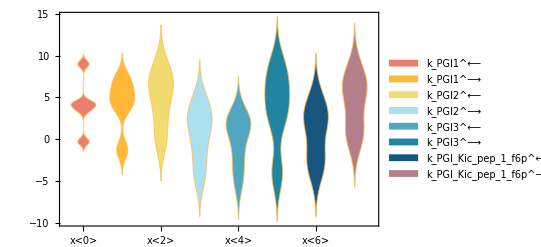

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

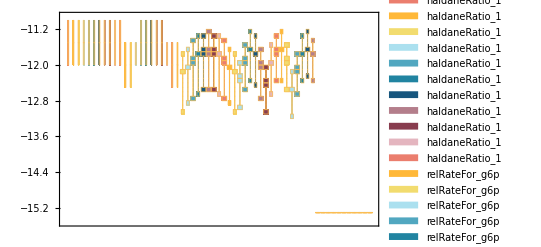

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.001018 | 6.12662×10^-18 (1.6616×10^14+6.39077×10^17 pep^c) | 98231.8 Abs[0.001018-6.12662×10^-18 (1.6616×10^14+6.39077×10^17 pep^c)]
0.000078 | 1.19406×10^-18 (6.53235×10^13+2.51244×10^17 pep^c) | 1.28205×10^6 Abs[0.000078-1.19406×10^-18 (6.53235×10^13+2.51244×10^17 pep^c)]

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.364 | 0.364 | 2.17287×10^-10